Лабораторная работа №7

Вариант №16. Толстихин Илья, 0В91
	Граф  G задан списком  ребер E с указанием веса ребра. Требуется, в соответствии с вариантом задания:
1.  Построить граф;
2.  Раскрасить граф, используя минимальное количество цветов;
2.  Найти кратчайший остов графа, полагая длину ребра, равной весу ребра;
3.  Считая, что множество E есть множество ориентированных ребер с пропускной способностью, равной весу ребра, а G - сетевой граф с источником в вершине V1 и стоком в вершине V45, найти максимальный поток в сети и указать минимальный (минимальные) разрез(ы) сети.

E={{1,2,7},{1,3,8},{1,5,6},{1,8,4},{1,10,10},{1,11,4},{1,14,4},{2,12,4},{2,14,6},{3,12,4},{3,13,8},{5,17,9},{5,22,5},{8,12,12},{8,13,8},{8,17,8},{8,21,5},{10,11,8},{10,21,10},{11,14,7},{11,19,7},{11,23,8},{12,15,12},{13,17,10},{13,19,11},{14,16,12},{14,20,9},{14,22,6},{14,25,12},{15,28,12},{15,32,3},{15,43,5},{16,19,12},{16,26,5},{17,20,4},{17,25,4},{17,32,8},{19,21,7},{19,30,11},{19,31,9},{20,26,4},{20,29,12},{21,28,10},{21,30,4},{21,32,10},{22,31,12},{23,30,12},{23,34,6},{25,32,9},{25,40,7},{26,33,10},{26,37,4},{28,30,10},{28,33,12},{29,37,12},{29,45,3},{30,31,9},{30,41,8},{30,42,7},{31,34,6},{31,36,5},{31,43,7},{32,33,11},{32,44,4},{32,45,12},{33,40,6},{33,42,9},{33,44,4},{34,36,6},{36,41,5},{36,45,7},{37,44,9},{40,45,8},{41,45,4},{42,45,5},{43,45,8},{44,45,6}
Задание 1.  Граф в виде списка ребер

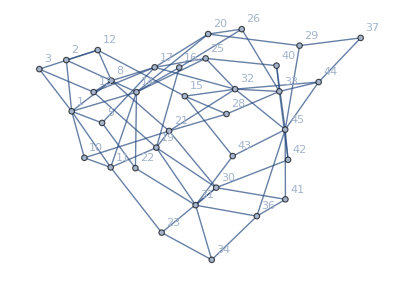

```mathematica
G=Graph[{1<->2,1<->3,1<->5,1<->8,1<->10,1<->11,1<->14,2<->12,2<->14,3<->12,3<->13,5<->17,5<->22,8<->12,8<->13,8<->17,8<->21,10<->11,10<->21,11<->14,11<->19,11<->23,12<->15,13<->17,13<->19,14<->16,14<->20,14<->22,14<->25,15<->28,15<->32,15<->43,16<->19,16<->26,17<->20,17<->25,17<->32,19<->21,19<->30,19<->31,20<->26,20<->29,21<->28,21<->30,21<->32,22<->31,23<->30,23<->34,25<->32,25<->40,26<->33,28<->33,29<->37,29<->45,30<->31,30<->41,30<->42,31<->34,31<->36,31<->43,32<->33,32<->44,32<->45,33<->40,33<->42,33<->44,34<->36,36<->41,36<->45,37<->44,40<->45,41<->45,42<->45,43<->45,44<->45},EdgeWeight->{1<->2->7,1<->3->8,1<->5->6,1<->8->4,1<->10->10,1<->11->4,1<->14->4,2<->12->4,2<->14->6,3<->12->4,3<->13->8,5<->17->9,5<->22->5,8<->12->12,8<->13->8,8<->17->8,8<->21->5,10<->11->8,10<->21->10,11<->14->7,11<->19->7,11<->23->8,12<->15->12,13<->17->10,13<->19->11,14<->16->12,14<->20->9,14<->22->6,14<->25->12,15<->28->12,15<->32->3,15<->43->5,16<->19->12,16<->26->5,17<->20->4,17<->25->4,17<->32->8,19<->21->7,19<->30->11,19<->31->9,20<->26->4,20<->29->12,21<->28->10,21<->30->4,21<->32->10,22<->31->12,23<->30->12,23<->34->6,25<->32->9,25<->40->7,26<->33->10,28<->33->4,29<->37->10,29<->45->12,30<->31->12,30<->41->3,30<->42->9,31<->34->8,31<->36->7,31<->43->6,32<->33->5,32<->44->7,32<->45->11,33<->40->4,33<->42->12,33<->44->6,34<->36->9,36<->41->4,36<->45->6,37<->44->5,40<->45->7,41<->45->9,42<->45->8,43<->45->4,44<->45->5},VertexLabels->"Name"]
```

```mathematica
num:=VertexList[G];colors:={Purple,Green,Red,Blue,Yellow}
```

```mathematica
For[Col=1,Col≤Length[colors],Col++,{
c:={}; t:=0,
For[i=1,i≤ Length[num],i++,{t:=0,
{For[j=1,j≤ Length[AdjacencyList[G,Part[num,i]]],j++,
If[Count[c,Part[AdjacencyList[G,Part[num,i]],j]]≠0,t=t+1]],

If[t==0,c=Join[colored,{Part[num,i]}] ,t=0]}}],
For[l=1,l≤ Length[c],l++,
num=Select[num,#!=Part[c,l]&]],

For[k=1,k≤ Length[c],k++,
G=Graph[G,VertexStyle->{Part[colored,k]->Part[c,Col]}]]}]
```

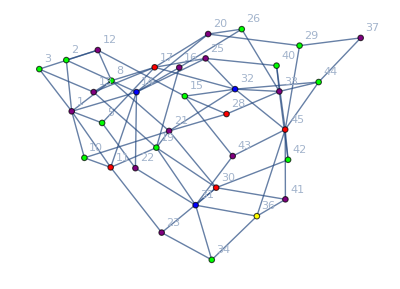

```mathematica
G
```

Задание 3.

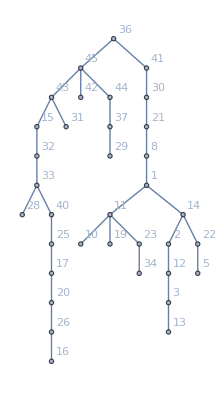

```mathematica
FindSpanningTree[G]
```

Задание 4.

```mathematica
FindMaximumFlow[G,1,45]
```

7

```mathematica
FindMinimumCut[G]
```

{15,{{1,2,3,5,8,10,11,14,12,13,17,22,21,19,23,15,16,20,25,28,32,43,26,30,31,29,34,40,33,45,41,42,36,44},{37}}}